```mathematica
ClearAll["Global`*"]
```

```mathematica
IP[ts_,λ_,σ_,ρ_,μ_,α_,β_,ϵ_,F0_,H0_,R0_] :=ItoProcess[{
ⅆF[t]== ts*((λ*F[t]-σ*(1-R[t])*F[t] + ρ*R[t]*H[t])ⅆt ),
ⅆH[t]== ts*((σ*(1-R[t])*F[t] - ρ*R[t]*H[t] - μ*H[t])ⅆt) ,
ⅆR[t]==ts*((α*ⅆt+ϵ*ⅆW[t])*R[t]*(1-R[t]) - R[t]*(ρ*H[t] + β*F[t])ⅆt)},
{F[t],H[t],R[t]},
{{F,H,R},{F0,H0,R0}},
t,
W\[Distributed]WienerProcess[]
]
```

```mathematica
stochsol[T_,TSlice_,Iterations_,ts_, λ_,σ_,ρ_,μ_,α_,β_,ϵ_,F0_,H0_,R0_]:=RandomFunction[IP[ts, λ,σ,ρ,μ,α,β,ϵ,F0,H0,R0],{0,T,TSlice},Iterations,Method->"KloedenPlatenSchurz"];
TD = With[{
T=500,
TSlice=0.1,
Iterations=1,
ts=1,
λ=0.2,
σ=2,
ρ=0.4,
μ=0.2,
α=0.5,
β=0.2,
ϵ=0.2},
Table[stochsol[T,TSlice,Iterations,ts,λ,σ,ρ,μ,α,β,ϵ,RandomReal[{0.2,1}],RandomReal[{0.2,1}],RandomReal[{0.2,1}]]["PathComponents"],{5}]
];
```

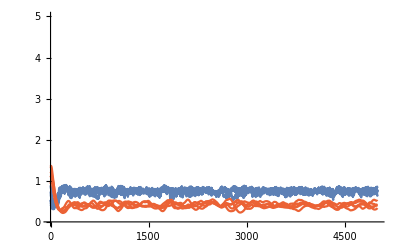

```mathematica
Show[{
(*Table[ListLinePlot[TD[[i]][[1]][[2]][[1]][[1]],PlotRange->{0,5},PlotStyle->ColorData[97,3]],{i,1,5,1}],
Table[ListLinePlot[TD[[i]][[2]][[2]][[1]][[1]],PlotRange->{0,5},PlotStyle->ColorData[97,2]],{i,1,5,1}],*)
Table[ListLinePlot[TD[[i]][[3]][[2]][[1]][[1]],PlotRange->{0,5},PlotStyle->ColorData[97,1]],{i,1,5,1}],
Table[ListLinePlot[TD[[i]][[1]][[2]][[1]][[1]]+TD[[i]][[2]][[2]][[1]][[1]],PlotRange->{0,5},PlotStyle->ColorData[97,4]],{i,1,5,1}]
}]
```

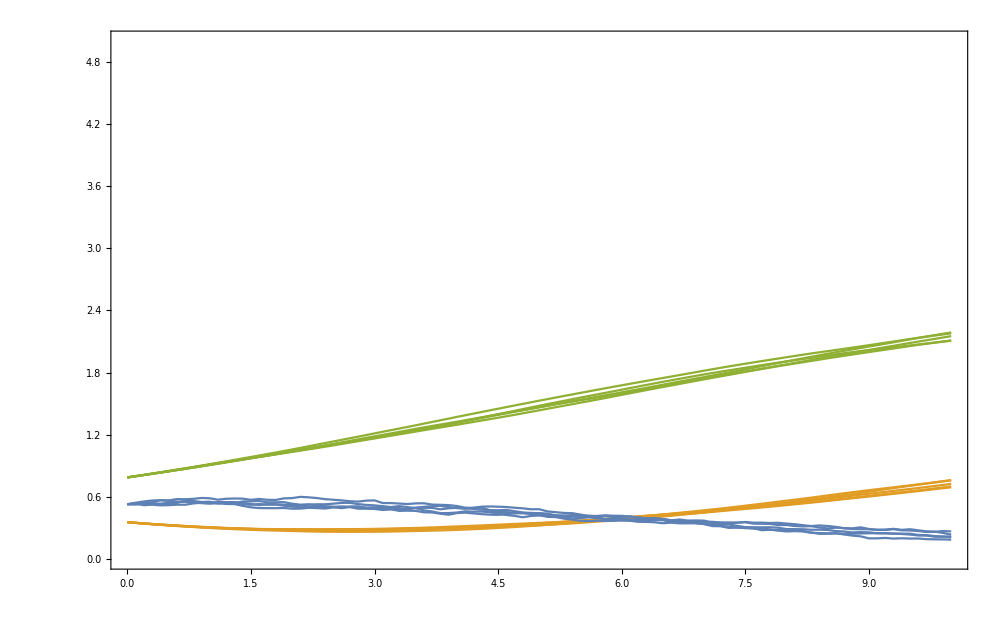

```mathematica
Show[{Table[ListLinePlot[TD[[i]],PlotStyle->ColorData[97,4-i],PlotRange->{0,5},Frame->True],{i,1,3}]}]
```

```mathematica
TD[[1]][[2]][[1]][[5]]+TD[[2]][[2]][[1]][[5]]
```

```mathematica
TestThreshold[timeseries_,threshold_]:=If[AnyTrue[timeseries,#<threshold&],1,0];
IPSigma[ts_,λ_,σ_,ρ_,μ_,α_,β_,ϵ_,F0_,H0_,R0_] :=ItoProcess[{
ⅆF[t]== ts*((λ*F[t]-σ*(1-R[t])*F[t] + ρ*R[t]*H[t])ⅆt ),
ⅆH[t]== ts*((σ*(1-R[t])*F[t] - ρ*R[t]*H[t] - μ*H[t])ⅆt) ,
ⅆR[t]==ts*((α*ⅆt+ϵ*ⅆW[t])*R[t]*(1-R[t]) - R[t]*(ρ*H[t] + β*F[t])ⅆt)},
{F[t],H[t],R[t]},
{{F,H,R},{F0,H0,R0}},
t,
W\[Distributed]WienerProcess[]
];
stochsol[T_,TSlice_,Iterations_,ts_, λ_,σ_,ρ_,μ_,α_,β_,ϵ_,F0_,H0_,R0_]:=RandomFunction[IPSigma[ ts,λ,σ,ρ,μ,α,β,ϵ,F0,H0,R0],{0,T,TSlice},Iterations,Method->"KloedenPlatenSchurz"];
(*sigvalues = RecurrenceTable[{sig[n+1] == sig[n]+1/2sig[n],sig[1]==0.0000001},sig,{n,1,53}];*)
sigvalues =Table[x,{x,0.21,2.01,0.1}];
ExtinctSigma=ParallelTable[
With[{
T=500,
TSlice=0.1,
Iterations=1,
ts=1,
λ=0.2,
σ=sigma,
ρ=0.4,
μ=0.2,
α=0.5,
β=0.2,
ϵ=0.2,
Its=1000,
Min0=0.5},
TD =Table[stochsol[T,TSlice,Iterations,ts,λ,σ,ρ,μ,α,β,ϵ,RandomReal[{Min0,1}],RandomReal[{Min0,1}],RandomReal[{Min0,1}]]["PathComponents"],{Its}];
Extinct=Table[
consumerdensity=TD[[it]][[1]][[2]][[1]][[1]]+TD[[it]][[2]][[2]][[1]][[1]];
TestThreshold[consumerdensity,0.4(**Mean[consumerdensity]*)],
{it,1,Its,1}];
{N[sigma/ρ],N[Total[Extinct]/Its]}
],
{sigma,sigvalues}];
```

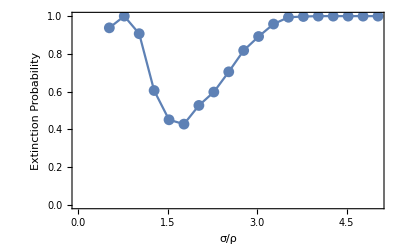

```mathematica
TroughPlot=
Show[{
ListPlot[ExtinctSigma,PlotRange->{0,1},Frame->True,FrameLabel->{"σ/ρ","Extinction Probability"}],
ListLinePlot[ExtinctSigma,PlotRange->{0,1}]
}]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_Extinction.pdf",TroughPlot,"PDF",ImageResolution->300]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_Extinction.pdf

Range over multiple values of epsilon

```mathematica
Ratesfunc[x_] :=(
noise=x[[1]];
ts=x[[2]];
M=x[[3]];
B0=x[[4]];
Bm=x[[5]];
Em=x[[6]];
η=x[[7]];
η2=x[[8]];
λ0=x[[9]];
ef=x[[10]];
γ=x[[11]];
ζ=x[[12]];
f0=x[[13]];
mm0=x[[14]];
growth =N[ts* λ0*M^η2]*(1+RandomReal[{-noise,noise}]) ;
starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])]*(1+RandomReal[{-noise,noise}]);
mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])]*(1+RandomReal[{-noise,noise}]);
recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
maintenance = (ts*ef*B0*M^η)*(1+RandomReal[{-noise,noise}]);
resourcegrowth = ts*0.5*(1+RandomReal[{-noise,noise}]);

{growth,starvation,mortality,recovery,maintenance,resourcegrowth}
)
```

```mathematica
Remove[Mass];
RatesByMass =
Table[
parameters={
(*noise*)0.2,
(*ts*)1000,
(*M*)Mass =10^(y+RandomReal[{-0.05,0.05}]),
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324};
R=Ratesfunc[parameters];
{Mass,R},
{y,-2,7,0.01}];
```

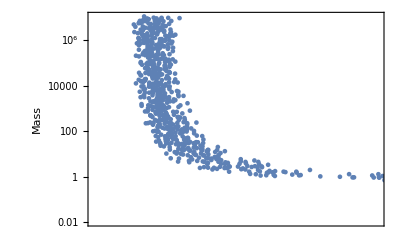

```mathematica
SigmaRhoMassFig = ListLogPlot[Transpose[{RatesByMass[[All,2]][[All,2]]/RatesByMass[[All,2]][[All,4]],RatesByMass[[All,1]]}],Frame->True,FrameTicks->{None,Automatic,Automatic,Automatic},FrameLabel->{"","Mass"},PlotRange->{{0,5},{0,All}},ImageSize->400]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
TestThreshold[timeseries_,threshold_]:=If[AnyTrue[timeseries,#<threshold&],1,0];
IPSigma[ts_,λ_,σ_,ρ_,μ_,α_,β_,ϵ_,F0_,H0_,R0_] :=ItoProcess[{
ⅆF[t]== ts*((λ*F[t]-σ*(1-R[t])*F[t] + ρ*R[t]*H[t])ⅆt ),
ⅆH[t]== ts*((σ*(1-R[t])*F[t] - ρ*R[t]*H[t] - μ*H[t])ⅆt) ,
ⅆR[t]==ts*((α*ⅆt+ϵ*ⅆW[t])*R[t]*(1-R[t]) - R[t]*(ρ*H[t] + β*F[t])ⅆt)},
{F[t],H[t],R[t]},
{{F,H,R},{F0,H0,R0}},
t,
W\[Distributed]WienerProcess[]
];
stochsol[T_,TSlice_,Iterations_,ts_, λ_,σ_,ρ_,μ_,α_,β_,ϵ_,F0_,H0_,R0_]:=RandomFunction[IPSigma[ ts,λ,σ,ρ,μ,α,β,ϵ,F0,H0,R0],{0,T,TSlice},Iterations,Method->"KloedenPlatenSchurz"];
(*sigvalues = RecurrenceTable[{sig[n+1] == sig[n]+1/2sig[n],sig[1]==0.0000001},sig,{n,1,53}];*)
sigvalues =Table[x,{x,0.21,2.01,0.1}];
epsilonvalues =Table[x,{x,0,0.5,0.1}];
ExtinctSigmaEpsilon=ParallelTable[
With[{
T=500,
TSlice=0.1,
Iterations=1,
ts=1,
λ=0.2,
σ=sigma,
ρ=0.4,
μ=0.2,
α=0.5,
β=0.2,
ϵ=epsilon,
Its=1000,
Min0=0.5},
TD =Table[stochsol[T,TSlice,Iterations,ts,λ,σ,ρ,μ,α,β,ϵ,RandomReal[{Min0,1}],RandomReal[{Min0,1}],RandomReal[{Min0,1}]]["PathComponents"],{Its}];
Extinct=Table[
consumerdensity=TD[[it]][[1]][[2]][[1]][[1]]+TD[[it]][[2]][[2]][[1]][[1]];
TestThreshold[consumerdensity,0.4(**Mean[consumerdensity]*)],
{it,1,Its,1}];
{N[sigma/ρ],N[Total[Extinct]/Its]}
],
{sigma,sigvalues},{epsilon,epsilonvalues}];
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/ExtinctSigmaEpsilon.dat",ExtinctSigmaEpsilon]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Mathematica/ExtinctSigmaEpsilon.dat

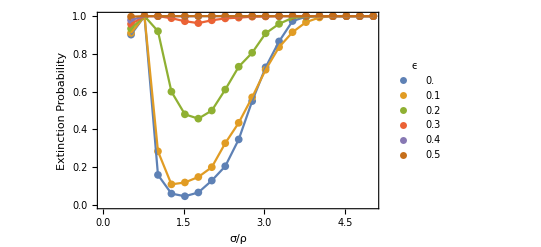

```mathematica
TroughPlotES=Show[{
ListPlot[Table[ExtinctSigmaEpsilon[[All,i]],{i,1,Length[epsilonvalues],1}],PlotRange->{0,1},Frame->True,FrameLabel->{"σ/ρ","Extinction Probability"},PlotLegends->Placed[PointLegend[epsilonvalues,LegendLabel->"ϵ"],{Right,Bottom}]],
ListLinePlot[Table[ExtinctSigmaEpsilon[[All,i]],{i,1,Length[epsilonvalues],1}]]
},ImageSize->400]
```

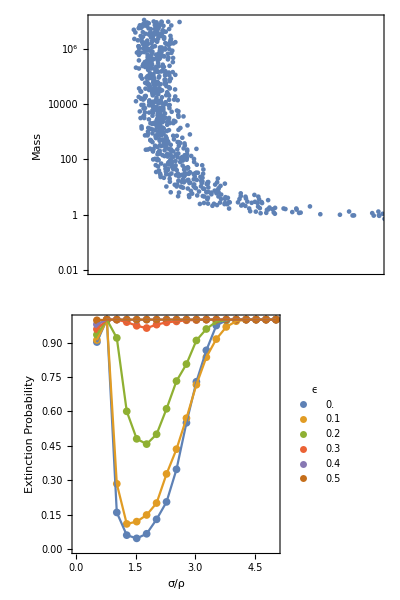

```mathematica
ExtinctionSigmaRho=Labeled[Column[{SigmaRhoMassFig,TroughPlotES},Spacings->-0.65],
""]
```

```mathematica
Export["/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_ExtinctionES.pdf",ExtinctionSigmaRho,"PDF",ImageResolution->300]
```

/Users/justinyeakel/Dropbox/PostDoc/2014_DiffusingForager/DiffusingForager/Manuscript/fig_ExtinctionES.pdf

The non-stochastic version... across sigma and rho

```mathematica
ClearAll["Global`*"]
```

```mathematica
Ratesfunc[x_] :=(
noise=x[[1]];
ts=x[[2]];
M=x[[3]];
B0=x[[4]];
Bm=x[[5]];
Em=x[[6]];
η=x[[7]];
η2=x[[8]];
λ0=x[[9]];
ef=x[[10]];
γ=x[[11]];
ζ=x[[12]];
f0=x[[13]];
mm0=x[[14]];
growth =N[ts* λ0*M^η2]*(1+RandomReal[{-noise,noise}]) ;
starvation =  N[ts*-Bm/(Em*Log[1-f0*M^(γ-1)])]*(1+RandomReal[{-noise,noise}]);
mortality =N[ts*-Bm/(Em*Log[1-(f0*M^γ+ mm0*M^ζ)/M])]*(1+RandomReal[{-noise,noise}]);
recovery =N[ ts*- ((η-1)*Bm/Em)/(Log[1-(M*(B0/Bm)^(1/(η-1)))^(1-η)]-Log[1 - (M*(1-f0*M^(γ-1))*(B0/Bm)^(1/(η-1)))^(1-η)])]*(1+RandomReal[{-noise,noise}]);
maintenance = (ts*ef*B0*M^η)*(1+RandomReal[{-noise,noise}]);
resourcegrowth = ts*0.5*(1+RandomReal[{-noise,noise}]);

{growth,starvation,mortality,recovery,maintenance,resourcegrowth}
)
```

```mathematica
parameters={
(*noise*)0,
(*ts*)1,
(*M*)Mass =10^3,
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324};
Ratesfunc[parameters]
```

{8.16452×10^-8,0.0000293632,4.17596×10^-6,0.000025274+0. ⅈ,0.00337873,0.5}

```mathematica
MetapopDyn[α_,λ_,σ_,ρ_,β_,μ_,T_,F0_,H0_,R0_] :=

NDSolve[{
F'[t] ==λ*F[t]-σ*(1-R[t])*F[t] +ρ* R[t] * H[t],
H'[t] ==σ*(1-R[t])*F[t] - ρ* R[t]*H[t] - μ*H[t],
R'[t] ==α*R[t]*(1-R[t]) -(ρ*H[t] + β*F[t])*R[t] ,
F[0]==F0,H[0]==H0,R[0]==R0},{F,H,R},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];
TestThreshold[timeseries_,threshold_]:=If[AnyTrue[timeseries,#<threshold&],1,0];
```

```mathematica
rhovalues = Table[x,{x,0.2,0.7,0.1}];
sigmavalues = Table[x,{x,0.3,2,0.1}];
ExtinctionSigma = ParallelTable[
Reps = 500;
ProportionExtinct=With[{
α=0.5,λ=0.2,σ=sigma,ρ=rho,β=0.2,μ=0.2,T=1000,threshold=0.4},
ExtinctionReps = Table[
F0=RandomReal[{threshold,1}];
H0 = RandomReal[{threshold,1}];
R0 = RandomReal[{threshold,1}];
(*Traj=Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,T,F0,H0,R0] ]*)
Traj=Table[Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,T,F0,H0,R0]],{t,0,200,.1}];
Ftraj = Flatten[Traj,1][[All,1]];
Htraj = Flatten[Traj,1][[All,2]];
Rtraj = Flatten[Traj,1][[All,3]];
ConsumerDensity = Htraj + Ftraj;
Extinct=TestThreshold[ConsumerDensity,threshold],
{Reps}];
{sigma/rho,N[Total[ExtinctionReps]/Reps]}
],
{sigma,sigmavalues},{rho,rhovalues}];
```

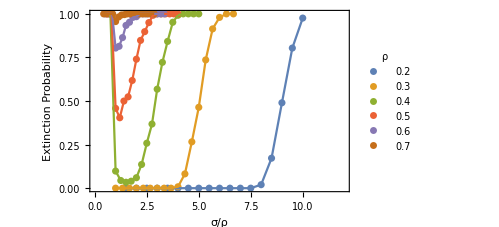

```mathematica
Show[{
ListPlot[Table[ExtinctionSigma[[All,i]],{i,1,Length[rhovalues],1}],PlotRange->{{0,12},{0,1}},Frame->True,FrameLabel->{"σ/ρ","Extinction Probability"},PlotLegends->Placed[PointLegend[rhovalues,LegendLabel->"ρ"],{Right,Bottom}]],
ListPlot[Table[ExtinctionSigma[[All,i]],{i,1,Length[rhovalues],1}],PlotRange->{0,1},Joined->True]
}]
```

```mathematica
Table[rho,{rho,0.2,0.8,0.2}]
```

{0.2,0.4,0.6,0.8}

USING REALISTIC (ALLOMETRIC) PARAMTER VALUES

```mathematica
MetapopDyn[α_,λ_,σ_,ρ_,β_,μ_,T_,F0_,H0_,R0_] :=

NDSolve[{
F'[t] ==λ*F[t]-σ*(1-R[t])*F[t] +ρ* R[t] * H[t],
H'[t] ==σ*(1-R[t])*F[t] - ρ* R[t]*H[t] - μ*H[t],
R'[t] ==α*R[t]*(1-R[t]) -(ρ*H[t] + β*F[t])*R[t] ,
F[0]==F0,H[0]==H0,R[0]==R0},{F,H,R},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];
TestThreshold[timeseries_,threshold_]:=If[AnyTrue[timeseries,#<threshold&],1,0];
parameters={
(*noise*)0,
(*ts*)1,
(*M*)Mass =10^2,
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.0000001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324};
RF =Ratesfunc[parameters];
growth=RF[[1]];
starvation=RF[[2]];
mortality=RF[[3]];
recovery=RF[[4]];
maintenance=RF[[5]];
resourcegrowth=RF[[6]];
With[{α=resourcegrowth*1,λ=growth,σ=starvation/2.5,ρ=recovery,β=maintenance,μ=mortality,T=100000000,F0=10000,H0=10000,R0=10000},
(*Traj=Evaluate[{R[t],H[t],F[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,T,F0,H0,R0] ];*)
Traj=Table[Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,T,F0,H0,R0]],{t,0,100000000,100000}];
(*ListPlot[Traj,{t,0,T},PlotRange->{0,All},AspectRatio->0.25,Frame->True,FrameLabel->{"Time","R,S,F"}]*)
]
```

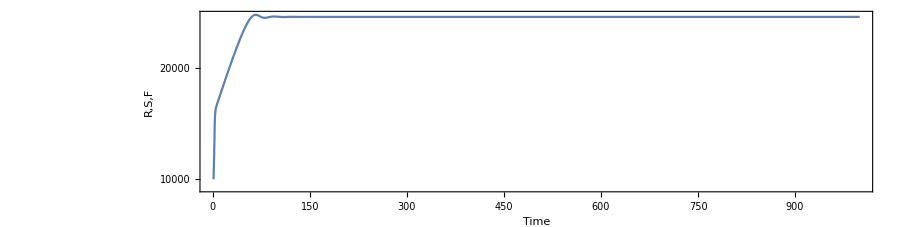

```mathematica
ListLogPlot[Flatten[Traj,1][[1;;1000,1]],PlotRange->All,AspectRatio->0.25,Frame->True,FrameLabel->{"Time","R,S,F"},Joined->True]
```

```mathematica
2.5*10^4
```

25000.

Extinction sims across realistic ranges of values

```mathematica
MetapopDyn[α_,λ_,σ_,ρ_,β_,μ_,T_,F0_,H0_,R0_] :=

NDSolve[{
F'[t] ==λ*F[t]-σ*(1-R[t])*F[t] +ρ* R[t] * H[t],
H'[t] ==σ*(1-R[t])*F[t] - ρ* R[t]*H[t] - μ*H[t],
R'[t] ==α*R[t]*(1-R[t]) -(ρ*H[t] + β*F[t])*R[t] ,
F[0]==F0,H[0]==H0,R[0]==R0},{F,H,R},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];
TestThreshold[timeseries_,threshold_]:=If[AnyTrue[timeseries,#<threshold&],1,0];
parameters={
(*noise*)0,
(*ts*)1,
(*M*)Mass =10^2,
(*B0*)1.9*10^(-2),
(*Bm*)0.0245,
(*Em*)21.39/2*1000(*J/gram*),
(*η*)3/4,
(*η2*)-0.206,
(*λ0*)3.3879*10^(-7),
(*ef*)0.0000001,
(*γ*)1.19,
(*ζ*)1.01,
(*f0*)0.0202,
(*mm0*)0.324};
RF =Ratesfunc[parameters];
growth=RF[[1]];
starvation=RF[[2]];
mortality=RF[[3]];
recovery=RF[[4]];
maintenance=RF[[5]];
resourcegrowth=RF[[6]];
(*rhovalues = Table[x,{x,0.2,0.7,0.1}];*)
scalevalues = Table[x,{x,6,1,-0.1}];
ExtinctionSigma = ParallelTable[
Reps = 1000;
ProportionExtinct=With[{
α=resourcegrowth,λ=growth,σ=starvation/scale,ρ=recovery,β=maintenance,μ=mortality,T=100000000,threshold=15000},
ExtinctionReps = Table[
F0=RandomReal[{1000,30000}];
H0 = RandomReal[{1000,30000}];
R0 = RandomReal[{1000,30000}];
(*Traj=Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,T,F0,H0,R0] ]*)
Traj=Table[Evaluate[{F[t],H[t],R[t]}/.MetapopDyn[α,λ,σ,ρ,β,μ,T,F0,H0,R0]],{t,0,100000000,100000}];
Ftraj = Flatten[Traj,1][[100;;1000,1]];
Htraj = Flatten[Traj,1][[100;;1000,2]];
Rtraj = Flatten[Traj,1][[100;1000,3]];
ConsumerDensity = Htraj + Ftraj;
Extinct=TestThreshold[ConsumerDensity,threshold],
{Reps}];
{(starvation/scale)/ρ,N[Total[ExtinctionReps]/Reps]}
],
{scale,scalevalues}(*,{rho,rhovalues}*)];
```

NDSolve::ndsz: At t == 307062., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 141643., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 5.43797×10^7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 4.78354×10^7, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {400000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {200000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {54400000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {47900000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {400000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {200000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {54400000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {47900000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {400000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {200000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {54400000} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {47900000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 8.1282×10^6, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 167792., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 457578., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 2.51444×10^7, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 201262., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 233821., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 23589.8, step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 301728., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 234402., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {300000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 222633., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 369406., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 280016., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {300000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 117396., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 317927., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 80808.1, step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {100000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 258785., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 393951., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 295141., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {300000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 242255., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 312696., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 194679., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {200000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 233759., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 328425., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 178228., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {200000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 166485., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 229156., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 210182., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {300000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 236270., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 306849., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

NDSolve::ndsz: At t == 262160., step size is effectively zero; singularity or stiff system suspected.

InterpolatingFunction::dmval: Input value {300000} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

NDSolve::ndsz: At t == 150821., step size is effectively zero; singularity or stiff system suspected.

NDSolve::ndsz: At t == 275694., step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

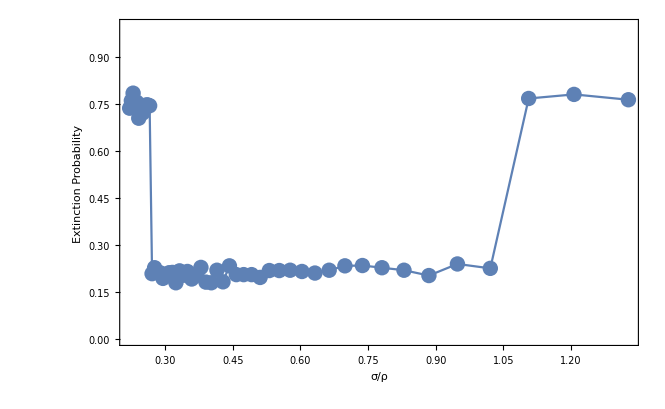

```mathematica
Show[{
ListPlot[ExtinctionSigma,PlotRange->{All,{0,1}},Frame->True,FrameLabel->{"σ/ρ","Extinction Probability"}],
ListPlot[ExtinctionSigma,PlotRange->{0,1},Joined->True]
}]
```

```mathematica
Log[0.7]
```

-0.356675